```mathematica
SetOptions[Plot, BaseStyle->{FontFamily->"Helvetica", FontSize->13},FrameStyle->Black, AspectRatio->Full];
makeSystem[A_, a_List,γ_List, ϵ_List]:=Module[{n=Length[A], varsV,varsw, lhsV, rhsV, lhsw, rhsw}, (*n here is the total number of heart cells*)
varsV=Table[Subscript[V, i][t],{i,1,n}];
varsw=Table[Subscript[w, i][t],{i,1,n}];
lhsV=D[varsV,t];
rhsV=Table[varsV[[i]](varsV[[i]]-a[[i]])(1-varsV[[i]])-varsw[[i]],{i,1,n}];
rhsV+=(A-DiagonalMatrix[Total/@A]).varsV;
lhsw=D[varsw,t];
rhsw=Table[varsV[[i]]-γ[[i]]varsw[[i]],{i,1,n}];

Join[Thread[lhsV==ϵ^-1 rhsV],Thread[lhsw==rhsw]]
]
makeSphereConnectionMatrix[n_,α_]:=Module[{i,j,k0, kEast, kWest, kNorth, kSouth}, (*n = size of the spatial grid => the total number of heart cells = n^2*)
getIndex[i_,j_]:=i n+j; (*get index of a heart cell given its position (row i, column j) in the spatial grid*)
A=Table[0,n^2,n^2];
Do[Do[
k =getIndex[i ,j]; (*index of the focal cell*)
kSouth=getIndex[Mod[i+1,n], j]; (*index of southern adjacent cell*)
kNorth=getIndex[Mod[i+n-1,n], j]; (*index of northern adjacent cell*)
kEast=getIndex[i, Mod[j+1,n]]; (*index of eastern adjacent cell*)
kWest=getIndex[i, Mod[j+n-1,n]]; (*index of western adjacent cell*)
A[[k+1,kSouth+1]]=α;
A[[k+1,kNorth+1]]=α;
A[[k+1,kEast+1]]=α;
A[[k+1,kWest+1]]=α
,{j, 0, n-1}],{i,0,n-1}];
SparseArray[A]
]

stimuliTrain[t_, A_,duty_, freq_]:=A*UnitBox[Mod[t*freq,1.]/(2. duty)]
stiGrid[τ_, s_List, S_List, n_]:= Module[{sm, i, j},
sm=Table[0,n,n];
Do[
i= Ceiling[s[[k]]/n];
j=Mod[s[[k]]-1, n]+1;
sm[[i, j]]=S[[k]]
,{k, 1, Length[s]}];
sm
]

spatialSim[A_, a_List,γ_List, ϵ_List, duration_, strength_, frequency_, sDelay_List, tmin_, tmax_, tStep_]:= Module[
{n=Sqrt[Length[A]],ODEsys, s, delay, S, vars,initLHS, init, solution, m, cellsPlots, stiPlots, dynamicPlots, staticPlots},
ODEsys = makeSystem[A, a, γ, ϵ];

s=sDelay[[1]]; delay=sDelay[[2]];
S=stimuliTrain[t+delay, strength, duration, frequency];
ODEsys[[s, 2]]+= S*ϵ[[1]]^-1;

(*Solve system*)
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];

staticPlots=Plot[Evaluate[{Subscript[V, 1][t],Subscript[V, n^2][t],Subscript[V, Ceiling[n^2/2]][t]}/.solution],{t,tmin,tmax},PlotRange->All,
			Frame->True, FrameLabel->{"t", "V"}, PlotLegends->{"V_1", Subscript["V", n^2], Subscript["V", Ceiling[n^2/2]]}];

m = Table[Subscript[V, (i-1) n+j][t]/.solution,{i,1,n},{j,1,n}];
cellsPlots= Table[MatrixPlot[m,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,
						ImageSize->400],{t,tmin,tmax,tStep}];
stiPlots = Table[MatrixPlot[stiGrid[t, {s}, {S}, n], ColorFunction->(ColorData[{"PigeonTones", "Reverse"}][Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False,
								ImageSize->400], 
					{t, tmin, tmax, tStep}];
dynamicPlots = Table[
Row[{
Column[{Style["Voltages of cells", FontSize->15], cellsPlots[[i]]}],
"    ", 
 Column[{Style["Stimulation", FontSize->15], stiPlots[[i]]}]
}], 
{i, 1, Length@cellsPlots}];

{staticPlots, dynamicPlots}
]

spatialSim2Sources[A_, a_List,γ_List, ϵ_List, duration_, strength_, frequency_, sDelay_List, tmin_, tmax_, tStep_]:= Module[
{n=Sqrt[Length[A]],ODEsys, s, delay, S, SS,vars,initLHS, init, solution, m, cellsPlots, stiPlots, dynamicPlots},
ODEsys = makeSystem[A, a, γ, ϵ];

S={};
Do[
s=sDelay[[k,1]]; delay=sDelay[[k,2]];
SS=stimuliTrain[t+delay, strength, duration, frequency];
S=AppendTo[S, SS];
ODEsys[[s, 2]]+= SS*ϵ[[1]]^-1
,{k, 1, Length[sDelay]}];

(*Solve system*)
vars = Integrate[ODEsys[[All, 1]], t];
initLHS =  vars/.t->tmin ;
init = Thread[initLHS== Table[0, Length@ODEsys]];
solution = NDSolve[{ODEsys, init}, vars, {t, tmin, tmax}][[1]];

m = Table[Subscript[V, (i-1) n+j][t]/.solution,{i,1,n},{j,1,n}];
cellsPlots= Table[MatrixPlot[m,ColorFunction->(ColorData["TemperatureMap"][Rescale[#,{-1,1}]]&),ColorFunctionScaling->False,
						ImageSize->400],{t,tmin,tmax,tStep}];
stiPlots = Table[MatrixPlot[stiGrid[t, sDelay[[All, 1]], S, n], ColorFunction->(ColorData[{"PigeonTones", "Reverse"}][Rescale[#,{0,0.2}]]&),ColorFunctionScaling->False,
								ImageSize->400], 
					{t, tmin, tmax, tStep}];
dynamicPlots = Table[
Row[{
Column[{Style["Voltages of cells", FontSize->15], cellsPlots[[i]]}],
"    ", 
 Column[{Style["Stimulation", FontSize->15], stiPlots[[i]]}]
}], 
{i, 1, Length@cellsPlots}];

{solution, dynamicPlots}
]
```

## 1 single cells receiving external stimulation

```mathematica
n=7; (*size of the spatial grid*)
cMatrix = makeSphereConnectionMatrix[n, 1/30];
MatrixForm[cMatrix];
aList = Table[0.01, Length@cMatrix];
γList = Table[0.5, Length@cMatrix];
ϵList = Table[0.008, Length@cMatrix];
duration=0.1;  strength=0.05 ;frequency=0.88;
tmin=0;
tmax=20;
tStep=0.05;
sDelay={1, 0.2};
sim1 = spatialSim[cMatrix, aList, γList, ϵList, duration, strength, frequency, sDelay, tmin, tmax, tStep];
```

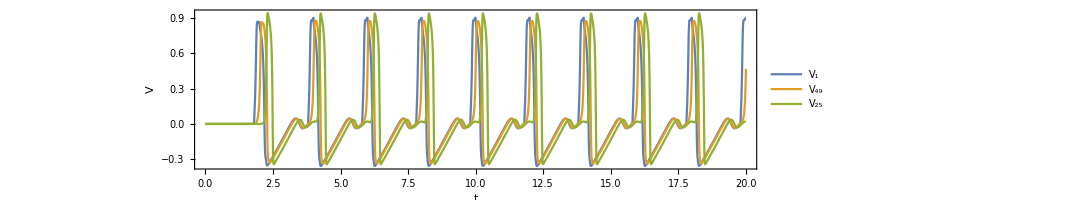
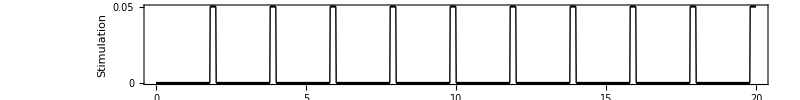
Simulation frequency = 0.5
-Graphics-
-Graphics-

```mathematica
ps = Plot[stimuliTrain[t+sDelay[[2]], strength, duration, frequency], {t, tmin, tmax},
PlotStyle->Black, ExclusionsStyle->True,
Frame->True, FrameLabel->{"t", "Stimulation"}];
Column[{
Row[{"Simulation frequency = ", Style[frequency, Bold]}, BaseStyle->{{FontFamily->"Helvetica"}, {FontSize->15}}],
Show[sim1[[1]], ImageSize->{800,200}],
 Show[ps, ImageSize->{800,100}, FrameTicks->{{{0, 0.025, 0.05},None},{{0, 5, 10, 15, 20}, None}}]
}]
```

```mathematica
ListAnimate[sim1[[2]]]
```

```mathematica
Export["./animation/FHN_spatial.1source.freq088.gif", sim1[[2]], "DisplayDurations"-> 0.1]
```

./FHN_spatial.1source.freq088.gif

## 2 cells receiving external stimulation

```mathematica
n=7; (*size of the spatial grid*)
cMatrix = makeSphereConnectionMatrix[n, 1/100];
MatrixForm[cMatrix];
aList = Table[0.01, Length@cMatrix];
γList = Table[0.5, Length@cMatrix];
ϵList = Table[0.008, Length@cMatrix];
duration=0.1;  strength=0.05 ;frequency=88/100;
tmin=0;
tmax=30;
tStep=0.05;
sDelay={{(2-1)n+2,1/frequency/20}, {(5-1)n+5, 1/frequency/7}};
sim2 = spatialSim2Sources[cMatrix, aList, γList, ϵList, duration, strength, frequency, sDelay, tmin, tmax, tStep];
```

```mathematica
ListAnimate[sim2[[2]]]
```

```mathematica
Export["./animation/FHN_spatial.2sources.coupling100.gif", sim2[[2]], "DisplayDurations"-> 0.1]
```

./FHN_spatial.2sources.coupling100.gif

```mathematica
ColorData[97,"ColorList"]
colorA = ColorData[97,"ColorList"][[{1, 10, 9, 15}]]
colorB = Join[ColorData[97,"ColorList"][[{8, 4}]], {Brown}]
colorC = {Pink, Gray}
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[1, 0.75, 0],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.6, 0.4, 0.2]}

{RGBColor[1, 0.5, 0.5],GrayLevel[0.5]}

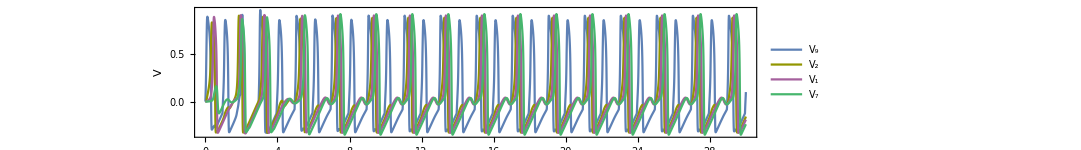
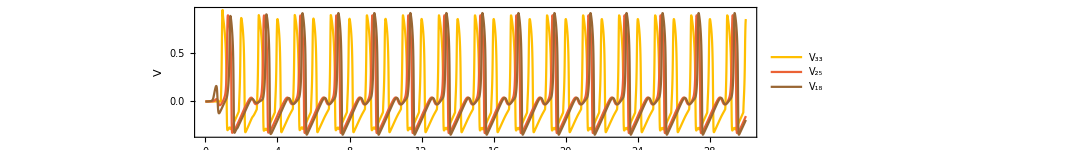
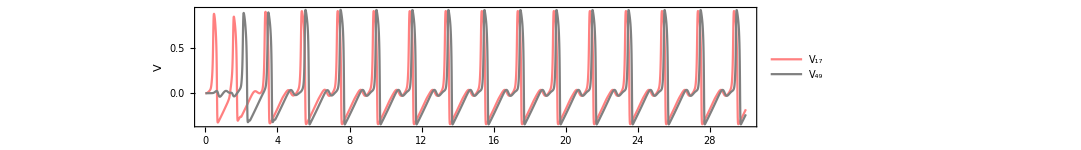
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
statPlotsA=Plot[Evaluate[{Subscript[V, 9][t],Subscript[V, 2][t],Subscript[V, 1][t], Subscript[V, 7][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorA,
			Frame->True, FrameLabel->{None, "V"}, PlotLegends->{"V_9", "V_2", "V_1", "V_7"}];
statPlotsB=Plot[Evaluate[{Subscript[V, 33][t],Subscript[V, 25][t],Subscript[V, 18][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorB,
			Frame->True, FrameLabel->{None, "V"}, PlotLegends->{"V_33", "V_25", "V_18"}];
statPlotsC=Plot[Evaluate[{Subscript[V, 17][t],Subscript[V, 49][t]}/.sim2[[1]]],{t,tmin,tmax},PlotRange->All,
			PlotStyle->colorC,
			Frame->True, FrameLabel->{"t", "V"}, PlotLegends->{"V_17", "V_49"}];

ps1 = Plot[stimuliTrain[t+sDelay[[1,2]], strength, duration, frequency], {t, tmin, tmax}, 
PlotStyle->colorA[[1]],ExclusionsStyle->colorA[[1]],
Frame->True, FrameLabel->{None, "Stimulation"}];
ps2 = Plot[stimuliTrain[t+sDelay[[2,2]], strength, duration, frequency], {t, tmin, tmax}, 
PlotStyle->colorB[[1]],ExclusionsStyle->colorB[[1]],
Frame->True, FrameLabel->{None, "Stimulation"}];

Column[{
Show[statPlotsA, ImageSize->{800,150}],
Show[ps1, ImageSize->{800,90}], 
Show[statPlotsB, ImageSize->{800,150}],
Show[ps2, ImageSize->{800,90}],
Show[statPlotsC, ImageSize->{800,150}]
}]
```

1.2

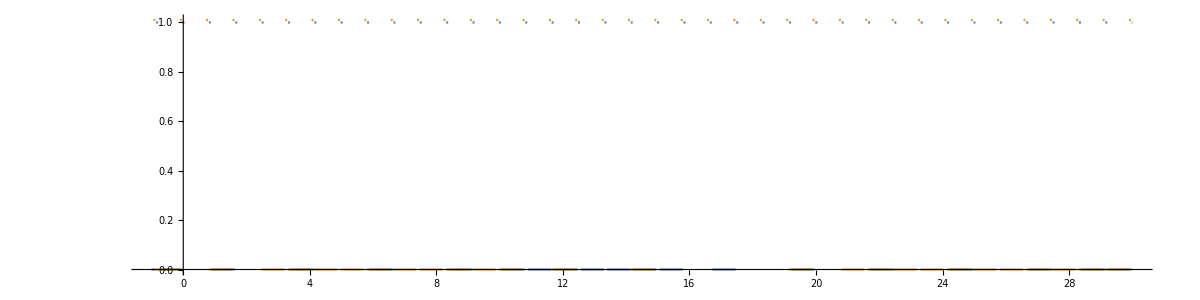

```mathematica
frequency=1.2
si1=stimuliTrain[t+1/frequency/25,1, duration, frequency];
si2=stimuliTrain[t+1/frequency/7,1.01, duration, frequency];
Plot[{si1, si2}, {t, tmin-1, tmax}, ImageSize->{1200, 300}, AspectRatio->Full]
```